```mathematica
Clear["Global`*"]
```

## 3 binding site model

We define a transition rate matrix for the “chain” model, which assumes 3 identical binding sites and, by construction is constrained to equilibrium. 
Such a model has 4 states, corresponding to the different numbers of TFs that may be bound. 

The only TF-TF interaction is captured by the  pair-wise “wm” term . If “n” TFs are bound, it is assumed that each TF is subjected to “n-1” pairwise 
interactions, and thus  the unbinding rate (“km”) is weighted by a factor “wm^(n-1)”

Note also that integer multipliers (eg the 3 in “3*kp”) account for multiplicity of molecular states. For instance, there are 3 distinct ways to bind one 
transcription factor starting from state 0 (because there are 3 sites).

```mathematica
Q3 = {{-3*kp ,          km,                                0,                                                 0 },
         {3*kp ,                     -km - 2*kp ,        2*km*wm,                                           0},
         {0,                                      2*kp,           -2*km*wm-kp ,                         3*wm^2*km},
  {0,                                      0,                               kp,                                        -3*wm^2*km}}/.kp->c*kp ;
```

```mathematica
MatrixForm[Q3]
```

(-3 c kp | km | 0 | 0
3 c kp | -km-2 c kp | 2 km wm | 0
0 | 2 c kp | -c kp-2 km wm | 3 km wm^2
0 | 0 | c kp | -3 km wm^2)

Check that the matrix is of proper form

```mathematica
Total[Q3]
```

{0,0,0,0}

### Plot Chain Model

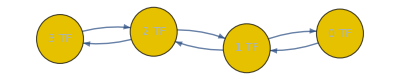

```mathematica
Graph[{"0 TF","1 TF","2 TF","3 TF"},ContinuousMarkovProcess[1,Q3],ImageSize->Small,GraphLayout->"SpringEmbedding"]
```

### Calculate steady-state occupancies for each state and assume “All-or-nothing” logic to obtain production rate

```mathematica
eigVectors = Eigenvectors[Q3];
```

```mathematica
steadyStateVec = FullSimplify[eigVectors[[1]] / Total[eigVectors[[1]]]];
```

```mathematica
pdRate = FullSimplify[steadyStateVec [[4]]]
```

(c^3 kp^3)/(c^3 kp^3+3 c^2 km kp^2 wm^2+km^2 (km+3 c kp) wm^3)

```mathematica
pdRate1 = (Numerator[pdRate ]/kp^3)/FullSimplify[(Denominator[pdRate]/kp^3)]
```

c^3/(c^3+(3 c^2 km wm^2)/kp+(km^2 (km+3 c kp) wm^3)/kp^3)

From this expression, we see that if wm is sufficiently small (if the cooperativity is sufficiently strong), then our system
should behave like a hill function of order 3

### Evaluate model for a reasonable set of parameter values

```mathematica
testVals = {kp->1,km->10,wm->0.01};
```

Define function to plot using test values

```mathematica
pdRateFun[c_] = pdRate/.testVals
```

c^3/(0.003 c^2+c^3+0.0001 (10+3 c))

Solve for half-max point (at Hill limit this will just be km*wm/kp)

```mathematica
hmSol =  Solve[pdRateFun[c]==0.5 && c>0,c,Reals];
```

```mathematica
KdEff = c/.hmSol[[1]]
```

0.10202

Define Hill functions for comparison

```mathematica
H3[c_] = c^3/(c^3 + KdEff^3);
```

```mathematica
H2[c_] = c^2/(c^2 + KdEff^2);
```

```mathematica
H1[c_] = c^1/(c^1 + KdEff);
```

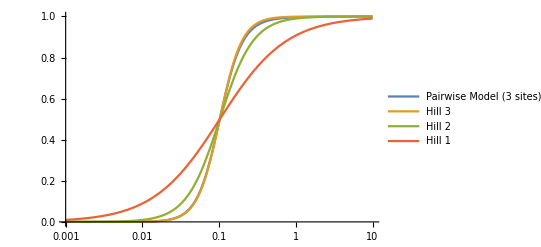

```mathematica
LogLinearPlot[{pdRateFun[c],H3[c],H2[c],H1[c]},{c,0.001,10},PlotRange->Automatic,PlotLegends->{"Pairwise Model (3 sites)","Hill 3","Hill 2","Hill 1"}]
```